## Teoría de la información cuántica Practica 2

I.1)

ψ=(0 …0+111 …1)/(√2)

ψ=((00…0)^m⊗(00…0)^(n-m)+(11…1)^m⊗(11…1)^(n-m))/(√2)

ψ=∑_(k=1)^n_s σ_k k_mk_(n-m)

```mathematica
Subscript[ρ, m]=∑_(k=1)^Subscript[n, s] Subscript[σ, k]^2 Subscript[k, m]Subscript[k, m];
```

```mathematica
Subscript[ρ, m]=1/2(Subscript[00…0, m] Subscript[00…0, m]+Subscript[11…1, m] Subscript[11…1, m]);
```

Para calcular de entropía utilizamos

```mathematica
S[x_]:=-Tr[x Log2[x]]
```

```mathematica
Subscript[ρ, m]=1/2({{1, 0}, {0, 1}});
```

```mathematica
S[Subscript[ρ, m]]
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

1

Para el estado

```mathematica
Φ=(10 …0+01 …0+…+0 …1)/(√n);
```

```mathematica
Φ=(Overscript[10 …0, m]⊗Overscript[00 …0, n-m]+01 …0⊗00 …0+…+00 …0⊗10 …0+…+00 …0⊗0 …1)/(√n);
```

Podemos tomar una base para el subespacio de los primeros m qubits y del subespacio de los n-m restantes respectivamente

```mathematica
i={Overscript[00 …0, m],01 …0,…,00 …1};
```

```mathematica
j={Overscript[00 …0, n-m],01 …0,…,00 …1};
```

Por lo tanto si escribimos

```mathematica
Φ=∑_ij^□ Subscript[c, ij] i j;
```

Obtenemos

```mathematica
Subscript[c, ij]=1/(√n)({{0, 1, 1, ⋯, 1}, {1, 0, 0, ⋯, 0}, {1, 0, 0, ⋯, 0}, {⋮, ⋮, ⋮, ⋱, 0}, {1, 0, 0, 0, 0}});
```

```mathematica
Rango[Subscript[C, ij]]=2;
```

Tomemos como ejemplo n=8 , m=3

```mathematica
Aij=1/(√8)({{0, 1, 1, 1, 1, 1}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}});
```

```mathematica
SingularValueDecomposition[Aij]
```

{{{1,0,0,0},{0,1/(√3),-1/(√2),-1/(√6)},{0,1/(√3),0,√(2/3)},{0,1/(√3),1/(√2),-1/(√6)}},{{(√(5/2))/2,0,0,0,0,0},{0,(√(3/2))/2,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,1,0,0,0,0},{1/(√5),0,-1/(√2),-1/(√6),-1/(2 √3),-1/(2 √5)},{1/(√5),0,0,0,0,2/(√5)},{1/(√5),0,0,0,(√3)/2,-1/(2 √5)},{1/(√5),0,0,√(2/3),-1/(2 √3),-1/(2 √5)},{1/(√5),0,1/(√2),-1/(√6),-1/(2 √3),-1/(2 √5)}}}

```mathematica
U={{1,0,0,0},{0,1/(√3),-1/(√2),-1/(√6)},{0,1/(√3),0,√(2/3)},{0,1/(√3),1/(√2),-1/(√6)}}//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1/(√3) | -1/(√2) | -1/(√6)
0 | 1/(√3) | 0 | √(2/3)
0 | 1/(√3) | 1/(√2) | -1/(√6))

```mathematica
Σ={{(√(5/2))/2,0,0,0,0,0},{0,(√(3/2))/2,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}//MatrixForm
```

((√(5/2))/2 | 0 | 0 | 0 | 0 | 0
0 | (√(3/2))/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
SuperPlus[V]={{0,1,0,0,0,0},{1/(√5),0,-1/(√2),-1/(√6),-1/(2 √3),-1/(2 √5)},{1/(√5),0,0,0,0,2/(√5)},{1/(√5),0,0,0,(√3)/2,-1/(2 √5)},{1/(√5),0,0,√(2/3),-1/(2 √3),-1/(2 √5)},{1/(√5),0,1/(√2),-1/(√6),-1/(2 √3),-1/(2 √5)}}//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
1/(√5) | 0 | -1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5)
1/(√5) | 0 | 0 | 0 | 0 | 2/(√5)
1/(√5) | 0 | 0 | 0 | (√3)/2 | -1/(2 √5)
1/(√5) | 0 | 0 | √(2/3) | -1/(2 √3) | -1/(2 √5)
1/(√5) | 0 | 1/(√2) | -1/(√6) | -1/(2 √3) | -1/(2 √5))

Para un n arbitrario tenemos

```mathematica
σ=({{√((n-m)/n), 0, 0, 0, 0, 0}, {0, √(m/n), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})
```

{{√((-m+n)/n),0,0,0,0,0},{0,√(m/n),0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

Por lo tanto la matriz de densidad reducida es

```mathematica
Subscript[ρ, m2]=({{(n-m)/n, 0}, {0, m/n}})
```

{{(-m+n)/n,0},{0,m/n}}

```mathematica
S[Subscript[ρ, m2]]
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

-(m Log[m/n])/(n Log[2])-((-m+n) Log[(-m+n)/n])/(n Log[2])

```mathematica
Simplify[-(m Log[m/n])/(n Log[2])-((-m+n) Log[(-m+n)/n])/(n Log[2])]
```

((m-n) Log[1-m/n]-m Log[m/n])/(n Log[2])

```mathematica
Manipulate[DiscretePlot[((m-n) Log[1-m/n]-m Log[m/n])/(n Log[2]),{m,1,n-1}],{n,2,100,1}]
```

```mathematica
S(Subscript[ρ, m2])=-1  [Log2[(n-m)/n]-m/n Log2[(n-m)/m]];
```

Set::write: Tag Times in S {{(-m+n)/n,0},{0,m/n}} is Protected.

## Compuertas Lógicas

```mathematica
0={1,0};
```

```mathematica
1={0,1};
```

```mathematica
0,0=TensorProduct[0,0]//Flatten 
0,1=TensorProduct[0,1]//Flatten
1,0=TensorProduct[1,0]//Flatten
1,1=TensorProduct[1,1]//Flatten
```

{1,0,0,0}

{0,1,0,0}

{0,0,1,0}

{0,0,0,1}

a) X ⊗ 𝕀

```mathematica
Subscript[X, A]=KroneckerProduct[PauliMatrix[1],IdentityMatrix[2]];
```

```mathematica
Subscript[X, A]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
Subscript[X, A]. 0,0
Subscript[X, A]. 0,1
Subscript[X, A]. 1,0
Subscript[X, A]. 1,1
```

{0,0,1,0}

{0,0,0,1}

{1,0,0,0}

{0,1,0,0}

```mathematica
Subscript[X, B]=KroneckerProduct[IdentityMatrix[2],PauliMatrix[1]];
```

```mathematica
Subscript[X, B]//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Subscript[X, B]. 0,0
Subscript[X, B]. 0,1
Subscript[X, B]. 1,0
Subscript[X, B]. 1,1
```

{0,1,0,0}

{1,0,0,0}

{0,0,0,1}

{0,0,1,0}

```mathematica
{0,1,0,0}
```

{0,1,0,0}

```mathematica
Subscript[X, AB]=KroneckerProduct[PauliMatrix[1],PauliMatrix[1]];
```

```mathematica
Subscript[X, AB]//MatrixForm
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
Subscript[X, AB]. 0,0
Subscript[X, AB]. 0,1
Subscript[X, AB]. 1,0
Subscript[X, AB]. 1,1
```

{0,0,0,1}

{0,0,1,0}

{0,1,0,0}

{1,0,0,0}

```mathematica
Subscript[U, x]=KroneckerProduct[KroneckerProduct[0,0],IdentityMatrix[2]]+KroneckerProduct[KroneckerProduct[1,1],PauliMatrix[1]];
```

```mathematica
Subscript[U, x]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Subscript[U, x]. 0,0
Subscript[U, x]. 0,1
Subscript[U, x]. 1,0
Subscript[U, x]. 1,1
```

{1,0,0,0}

{0,1,0,0}

{0,0,0,1}

{0,0,1,0}

U_x.0,0=0,0;
U_x.0,1=0,1;
U_x.1,0=1,1;
U_x.1,1=1,0;

Se verifica que U_x es un CNOT

```mathematica
Subscript[X, A].Transpose[Subscript[X, A]]//MatrixForm
Subscript[X, B].Transpose[Subscript[X, B]]//MatrixForm
Subscript[X, AB].Transpose[Subscript[X, AB]]//MatrixForm
Subscript[U, x].Transpose[Subscript[U, x]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

«1 more identical outputs»

2) Comprobar W=U_x(H⊗I) con H=(X+Z)/√2 la compuerta de hadamard . transforma la base computacional en la base de Bell. Determinando su representación matricial

```mathematica
W=Subscript[U, x]. KroneckerProduct[HadamardMatrix[2],IdentityMatrix[2]];
```

```mathematica
W//MatrixForm
```

(1/(√2) | 0 | 1/(√2) | 0
0 | 1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | 0 | -1/(√2)
1/(√2) | 0 | -1/(√2) | 0)

```mathematica
W. 0,0
W. 0,1
W. 1,0
W. 1,1
```

{1/(√2),0,0,1/(√2)}

{0,1/(√2),1/(√2),0}

{1/(√2),0,0,-1/(√2)}

{0,1/(√2),-1/(√2),0}

#### W.0,0= 1/(√2)(0,0+1,1) W.0,1=1/(√2)(0,1+1,0) W.1,0=1/(√2)(0,0-1,1) W.1,1=1/(√2)(0,1-1,0)

```mathematica
Subscript[β, 00]=W. 0,0;
Subscript[β, 01]=W. 0,1;
Subscript[β, 10]=W. 1,0;
Subscript[β, 11]=W. 1,1;
```

```mathematica
g=({{"C", 1, "C", "C"}, {1, 1, "Z", "N"}, {"C", "H", "N", 1}, {1, 1, "X", 1}});
```

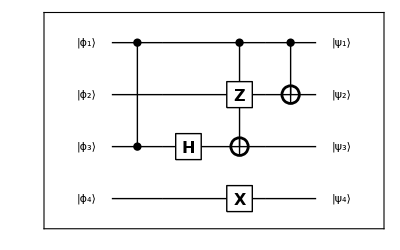

```mathematica
circuit[g]
```